# GCascade Tutorial Notebook

Welcome to the GCascade tutorial notebook. This notebook aims to walk through the basic functionality of the GCascade gamma-ray propagation package assuming very little prior knowledge of Mathematica. For information about the specific physics models used by the code, please refer to the documentation. To use this notebook simply follow the instructions, executing cells containing code by pressing (Shft + Enter).

## Importing and Setting Up The Package

### The following code adds the location of the package ( .wl file) to your "$Path" so that the Mathematica kernel knows where to find it when you try to import the package. Note that the “;” at the end of the expression prevents Mathematica from returning the output of a given command.

```mathematica
AppendTo[$Path, NotebookDirectory[]];
```

### Next, we import the package using the command short-hand “<<”. When the command is executed, the code within the package file is run in order to set up the internal functions and variables which are then made available in this notebook.

```mathematica
<<GCascadeV2.wl
```

You Have Imported GCascade. Setup will take about 2 minutes.

## Propagating Gamma-Rays

## Injected Spectrum

### The central input for GCascade is the injected spectrum. Formatting this array correctly is vital. Injected spectra should be lists of real numbers. The injected spectrum must be 300 members in length, i.e. as long as the list “energies”. The values in the injected spectrum are expected to be values of the injected differential flux spectrum evaluated at certain energies given by the list, “energies”. “energies” is a list of logarithmically spaced energies from 10^-1 GeV to 10^12 GeV, available from the GCascade package. As an example, below, the variable “injSpectrum” is assigned a list which is made using the function “Table”. Table takes in two inputs, a function, f(i), and an iterator, {i,i_start,i_final, di} , and returns a list, { f[i_start],f[i_start + di],...,f[i_final] }. We use “Table” to generate a list of the values of the function “cutoffPowerLaw” evaluated at the i-th member of the gamma-ray energy list, “energiesGamma[[i]]”. The function “cutoffPowerLaw[E,Γ,E_cutoff,A]” is a function that returns the value of an exponentially cutoff power law; dN/dE=A×E^-Γ exp[-E/E_cutoff]. Here, we choose to create a flat spectrum (i.e. Γ = 2) power law with a cutoff energy of 10^22 eV and a normalization of A = 3.12 x10^42 GeV^s^-1.

```mathematica
injSpectrum=Table[cutoffPowerLaw[energies[[i]],2.0,10^13,(3.12*10^42)],{i,1,Length[energies]}];
```

### This injected spectrum can be plotted as an energy spectrum using the “specPlot” function available in GCascade. The “specPlot” functions takes in a spectrum formatted as above and returns a primitive scatter plot of the energy spectrum, (E^2 dN/dE). The axes on the returned plot are given in units of GeV and GeV energy flux.

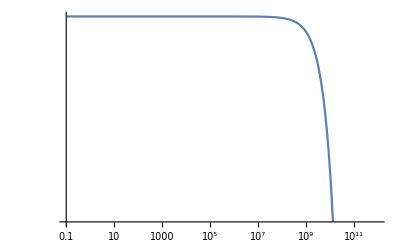

```mathematica
injectedPlot=specPlot[injSpectrum]
```

## Attenuation

### Suppose you want to calculate the resulting spectrum due to attenuation of some point source spectrum during cosmological transport. To simply attenuate the injected spectrum, you can use the “GAttenuate” function. “GAttenuate[injSpectra,zStart,stepSize]” is a function which takes in a gamma-ray injected spectrum, starting z, and step size in z. This function produces an attenuated differential spectrum, (dN/dE_γ (GeV^-1 cm^-2 s^-1)) , without including cascade evolution but taking into account cosmological energy shifts. The injected spectrum should be formatted as an array of values of differential flux (dN/dE_γ (GeV^-1 cm^-2 s^-1)) evaluated at the energies given by the array, energiesGamma. It is recommended to use a step size of up to (10^-5). Below, the variable, “attenuatedSpectrum” is assigned the output list of the function “CAttenuate”. “CAttenuate” is passed a differential spectrum (dN/dE_γ) which is injSpectrum. The injected spectrum is then allowed to propagate from Z = 0.001 in redshift steps of Δz=10^-5.

```mathematica
attenuatedSpectrum=GAttenuate[injSpectrum,0.001,10^-5];
attenuatedSpectrumPlot=specPlot[attenuatedSpectrum]
```

## EM Cascades From a Point Source

### Now, lets consider the cascade development during transport of the gamma-rays from the point source discussed in the example above. To calculate the spectrum after cascade development during transport from a point source, you can use the “GCascadePoint”. “GCascadePoint[injected spectrum, source distance (Z),step size (dZ)]” is one of two main functions of this program. GCascadePoint is a function which takes in a gamma-ray injected spectrum, source distance, and step size in Z. “GCascadePoint” produces a cascaded differential spectrum, (dN/dE (GeV^-1 s^-1)), taking into account cosmological and electromagnetic energy losses. It is recommended to use a step size of 10^-6. The injected differential spectrum (dN/dE) should be formatted as an array of values of power per unit area (GeV^-1 cm^-2 s^-1) evaluated at the energies given by the array, “energies”. Below, the variable, “pointSourceSpectrum” is assigned the output list of the function “GCascadePoint”. “GCascadePoint” is passed a differential spectrum (dN/dE_γ) which is injSpectrum. The injected energy spectrum is then allowed to propagate from Z = 0.001 in redshift steps of Δz=10^-6. This should take under a minute to run.

```mathematica
pointSourceSpectrum=GCascadePoint[injSpectrum,0.001,10^-6];
pointSourceSpectrumPlot=specPlot[pointSourceSpectrum]
```

## Diffuse Gamma-Ray Background from a Population of Sources

### Finally, we can consider the diffuse gamma-ray background from a class of sources, which have some intrinsic spectral properties and are distributed continuously as a function of redshift, z. to calculate the diffuse gamma-ray spectrum expected from such a class of sources, you can use the “GCascadeDiffuse” function. “GCascadeDiffuse[injected spectrum ,max Z (z_max),step size (dZ),Luminosity Function (ρ(z))]” is the other main functions of this program. “GCascadeDiffuse” is a function which takes in a gamma-ray injected luminosity spectrum, max z, step size in z, and a luminosity function. “GCascadeDiffuse” produces a cascaded diffuse differential spectrum, (dN/dE (GeV^-1 cm^-2 s^-1 sr^-1)) , taking into account cosmological and electromagnetic energy losses. It is recommended to use a step size of 10^-6. The Luminosity distribution function is assumed to be a separable function of the form: dN/(dV_c dE)(E_γ,z)=dN/dE_γ(E_γ)ρ(z) where the left-hand factor is the intrinsic differential spectrum of the class of sources (dN/dE_γ(GeV^-1 s^-1)) and ρ(z) is the spacial distribution of the sources in units of density per comoving volume, so called “luminosity function”. “GCascadeDiffuse” uses the luminosity function as an input which must be formatted as list of ordered pairs (z,ρ(z)), of values of z and comoving density ρ(z). The values of z can be any finite list of z from 0 to 10. GCascade provides two convenient lists of z, “zReg” and “diffuseDistance”. “zReg” is a list that contains values of z from 0 to 10 in increments of 0.01. “diffuseDistance” is a list that contains values of z from 0 to 10 in progressively increasing step sizes. “diffuseDistance” is the list of z-values used by the code to carry out the numerical integration (i.e. location of integration steps). This is a good list to use when ρ(z) is mainly localized near z=0. Below, the variable “diffuseBackgroundSpectrum” is assigned the output list of the function “GCascadeDiffuse”. “GCascadeDiffuse” is passed a differential luminosity spectrum (dN/dE_γ) which is “injSpectrum”. The Injected energy spectrum is then allowed to propagate from z = 0.1 in redshift steps of Δz=10^-6. The last input in the list is “ρ” and is created by first generating a list of size equal to “diffuseDistance”. The first 46 elements are set to the comoving number density, The list of z-values and ρ-values are then merged into ordered pair using the “Thread” function and assigned the variable “ρ”. This example evaluates the observed spectrum from a distribution of sources with a constant comoving number density of (5 x10^-6 Mpc^-3) out to a maximum z of 0.1. Note that the comoving number density must be converted to units of (cm^-3). Note that this calculation takes roughly 5-10 minutes to run. The “//Timing” command can be used after a line of code to obtain the computation time on that command.

```mathematica
Mpc = 3.086*10^24; (*cm*)
ρz=ConstantArray[0.0,Length[diffuseDistances]]; (*creates array*)
ρz[[1;;46]]=Table[5.0*10^-6*(Mpc)^-3,{i,1,46}]; (*sets the first 46 members*)
ρ=Thread[{diffuseDistances,ρz}];
diffuseBackgroundSpectrum=GCascadeDiffuse[injSpectrum,diffuseDistances[[46]],10^-6,ρ];//Timing
diffuseBackgroundSpectrumPlot=specPlot[diffuseBackgroundSpectrum]
```

## Data Output: Exporting and Polished Plots

## Exporting Data

### Suppose you’re trying to output a file which contains the data you’ve generated using GCascades. First, we make a list of ordered pairs consisting of gamma-ray energies and dN/dE_γ at those energies using the “thread” function. Then, we add to the beginning of that list a pair of informative data labels. Finally, the “Export” function is used to export this list into a “.csv” file which can be read universally. The code below uses the “Export” function which takes in two arguments, the first is the location and name of the file including the intended extension, the second is the data to export. Note that the location for export is set to use “NotebookDirectory”, which is the location of GCascade. To change this, simply replace the first argument with a valid file location which can be inserted using the “Insert > File Path” functionality in the menu above.

```mathematica
data=Thread[{energies,pointSourceSpectrum}];
data=Prepend[data,{"Gamma-Ray Energy (GeV)","Differential Spectrum dN/dE (GeV^-1 cm^-2 S^-1)"}];
Export[FileNameJoin[{NotebookDirectory[],"spectralDataExample.csv"}],data];
```

## The “Show” Function

### The “Show” function can be used to display and format any of the “Plot” primitives created in the previous examples. In the code below, we display the cascades point source spectrum, “pointSourceSpectrumPlot”, which is the first argument for the function “Show”. The proceeding arguments may also be changed in order to change aspects of the frame. Form more information about “Show” or “Plot”, use the Wolfram Mathematica documentation search function which can be found under the “help” tab in the menu above.

```mathematica
ticks={{Flatten[{Table[{10^x,("10")^ToString[x]},{x,-100,100}],Flatten[Table[{y*10^x,""},{y,2,9},{x,-100,100}],1]},1],None},
{Flatten[{{{0.1 ,"10^-1"}},{{1 ,"1"}},Table[{10^x,("10")^ToString[x]},{x,1,12,1}],Flatten[Table[{y*10^x,""},{y,2,9},{x,-100,100}],1]},1]
,None}};

p1=LogLogPlot[Interpolation[Thread[{energies,energies^2 attenuatedSpectrum}]][x],{x,10^-1,10^12},
PlotRange->{{0.1,10^6},{10^-11,10^-8}},
PlotStyle->{Red,Thick},
FrameTicks->ticks
];
p2=LogLogPlot[Interpolation[Thread[{energies,energies^2 pointSourceSpectrum}]][x],{x,10^-1,10^12},
PlotRange->{{0.1,10^6},{10^-11,10^-8}},
PlotStyle->{Blue,Thick},
FrameTicks->ticks
];

Show[p2,p1,
Axes->False,
Frame->True,
FrameStyle-> Thickness[0.004],
FrameTicksStyle-> Thickness[0.004],
FrameLabel->{{"E_γ^2dN/dE_γ (GeV cm^-2 s^-1)",None},{"E_γ (GeV)",None}},
LabelStyle-> Directive[Bold,Black,FontFamily-> "Helvetica",FontSize-> 14],
ImageSize->Large
]
```

## Advanced: Changing the Magnetic field

### While the intergalactic magnetic field is set by default to B=10^-13 G is is possible to change this value. However, due to the nature of the calculation, GCascade needs to reproduce all of its libraries in order to effect this change. This process will take around 30 minutes to complete. After the process is complete, you will need to open the package file and change the name of the libraries by changing the string “libraryNames” found directly under the variable “libraryLocation” which you’ve already customized. GCascade provides the function “changeMagneticField” which changes the magnetic field and produces the new libraries. the first argument is the magnetic field in Gauss and the second is a string which will be prepended to the default “libraryNames” string during export. Thus the final name of the libraries will start with whatever you pass as the second argument making it simple to change “libraryNames” in the package file by simply adding this string to the beginning. Finally you must import the package once again in order to have working functionality with the new magnetic field. It should be noted that changing the magnetic field to anything under about 0.1 nG will leave the calculation done here largely unchanged and will only affect the highest energies, E_e>10^19 eV. Thus, in general, it is not recommended to change the magnetic field.

```mathematica
changeMagneticField[10^-10,"Test"]
```

#### At this point you would go into the package “.wl” file and change “libraryNames” from the default “DiffCascadeSpectralTable” to “TestDiffCascadeSpectralTable” and save the file. Then, you would need to rerun the import command “<<GCascadeV2.wl” before running any new calculations with the new magnetic field.

```mathematica
<<GCascadeV2.wl
```